Evaluate NotebookDelete Output Cells

# Physics 114: Practical 3 (CPA)

#### Important:

You are reminded of the university’s plagiarism policy as detailed in the General Yearbook.

Parts of this practical is marked electronically. It is important that you read the questions carefully and always assign the final answer to a question (whether this is a number, an expression, a list, or a plot) to the variable corresponding to the question. Only provide numeric (decimal number) answers when asked. For example, do not replace Sin[2] by Sin[2.0] or 1/2 by 0.5 unless the question asks for it.  11052021

#### Deadline:

Submit you final Mathematica notebook file on SunLearn before 19:00 on Friday 14 May.

#### Consultation:

There will be an extra Teams consultation session from 13:00 to 14:00 on Thursday.

#### Clearing Definitions:

You can run the cell below to clear all the definitions currently in memory. Do not add extra ClearAll[“Global`*”] statements elsewhere in the file, as this will interfere with the marking.

```mathematica
Clear[Derivative]; ClearAll["Global`*"]; (*Run to clear all definitions.*)
studentnotebookdirectory=NotebookDirectory[];$HistoryLength=2;
```

#### Identify Yourself:

Change the name of the file to include your student number, surname and initials.

Assign your initials and surname (in quotes) and student number to the variables below.

```mathematica
StudentName="JL Gouws";
StudentNumber=26634554;
```

## Q: Examples

Calculate (23+9+1/2)/27^3. (Note that you must assign your final answer to the variable corresponding to the question.)

Q1

```mathematica
Q1=(23+9+1/2)/27^3
```

65/39366

Assign 23/6 to W and calculate W^3. (Note that you must assign your final answer to the variable corresponding to the question.)

Q2

```mathematica
W=23/6;
Q2=W^3
```

12167/216

## A: Basic Arithmetic

A1

```mathematica
A1=Sqrt[4084441]
```

2021

A2

```mathematica
A2=1481544^(1/3)
```

114

A3

```mathematica
A3=(13 * 2023)/(29 + 31)
```

26299/60

A4

```mathematica
A4=Sin[Pi/3]
```

(√3)/2

A5

```mathematica
A5=Sin[Degree * 60]
```

(√3)/2

A6

```mathematica
A6=Log[exp[7]]
```

Log[exp[7]]

A7

```mathematica
A7= Log[10, 10^4]
```

4

A8

```mathematica
A8=N[Exp[-Sin[Sqrt[7]]]]
```

0.621405

A9

```mathematica
A9=N[Pi^8,10]
```

9488.531016

A10

```mathematica
A10= Abs[-15]
```

15

A11

```mathematica
A11= Prime[26634554]
```

505593653

## B: Assignments

B1

```mathematica
mass = 173
velocity = 24
```

173

24

```mathematica
B1=1/2 * mass * velocity ^2
```

49824

## C: Symbolic Expressions

```mathematica
(*Run if you accidentally assigned values to x, y or z.*)
ClearAll[x,y,z];
```

C1

```mathematica
C1=Expand[(x + y + z)^6]
```

x^6+6 x^5 y+15 x^4 y^2+20 x^3 y^3+15 x^2 y^4+6 x y^5+y^6+6 x^5 z+30 x^4 y z+60 x^3 y^2 z+60 x^2 y^3 z+30 x y^4 z+6 y^5 z+15 x^4 z^2+60 x^3 y z^2+90 x^2 y^2 z^2+60 x y^3 z^2+15 y^4 z^2+20 x^3 z^3+60 x^2 y z^3+60 x y^2 z^3+20 y^3 z^3+15 x^2 z^4+30 x y z^4+15 y^2 z^4+6 x z^5+6 y z^5+z^6

C2

```mathematica
C2=Simplify[(1 + z)^2 + (1 + z)(2 + z)]
```

3+5 z+2 z^2

C3

```mathematica
C3=Factor[(1 + z)^2 + (1 + z)(2 + z)]
```

(1+z) (3+2 z)

C4

```mathematica
C4=Apart[x^14/(x^8 - 1)]
```

1/(8 (-1+x))+x^6-1/(8 (1+x))+1/(4 (1+x^2))+x^2/(2 (1+x^4))

C5

```mathematica
C5=Together[(x + 1)^2 / 15 + z/x^2]
```

(x^2+2 x^3+x^4+15 z)/(15 x^2)

## D: Lists

D1

```mathematica
D1={9, Cos[3], -3, 11}
```

{9,Cos[3],-3,11}

D2

```mathematica
D2=Table[3 * i, {i, 1, 27}]
```

{3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51,54,57,60,63,66,69,72,75,78,81}

D3

```mathematica
D3=D2[[17]]
```

51

D4

```mathematica
D4=Table[{n, Cos[n/3]}, {n, 0, 31}]
```

{{0,1},{1,Cos[1/3]},{2,Cos[2/3]},{3,Cos[1]},{4,Cos[4/3]},{5,Cos[5/3]},{6,Cos[2]},{7,Cos[7/3]},{8,Cos[8/3]},{9,Cos[3]},{10,Cos[10/3]},{11,Cos[11/3]},{12,Cos[4]},{13,Cos[13/3]},{14,Cos[14/3]},{15,Cos[5]},{16,Cos[16/3]},{17,Cos[17/3]},{18,Cos[6]},{19,Cos[19/3]},{20,Cos[20/3]},{21,Cos[7]},{22,Cos[22/3]},{23,Cos[23/3]},{24,Cos[8]},{25,Cos[25/3]},{26,Cos[26/3]},{27,Cos[9]},{28,Cos[28/3]},{29,Cos[29/3]},{30,Cos[10]},{31,Cos[31/3]}}

D5

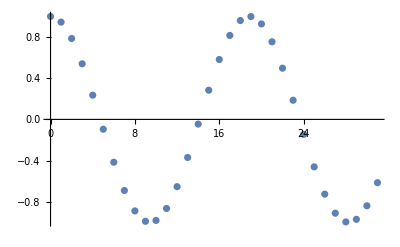

```mathematica
D5=ListPlot[D4]
```

D6

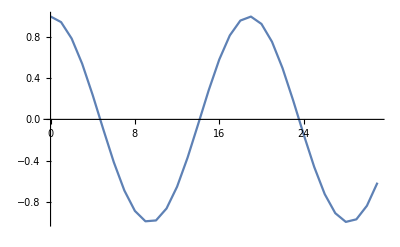

```mathematica
D6=ListLinePlot[D4]
```

## E: Replacement Rules and Algebraic Equations

```mathematica
(*Run if you accidentally assigned values to x and y.*)
ClearAll[x,y];
```

E1

```mathematica
E1=ReplaceAll[x^4 + x *  y^2 + (y-2)^2, {x -> 5, y -> -8}]
```

1045

E2

```mathematica
E2=Solve[x^3 - 2 * x^2 - 119 * x == 312]
```

{{x→-8},{x→-3},{x→13}}

E3

```mathematica
E3=Replace[x,E2[[3]]]
```

13

E4

```mathematica
E4=ReplaceAll[Sqrt[x ^ 2 + y ^2], Solve[{2 * x - 4 * y == 1, 4 * x + 2 * y == -28}][[1]]]
```

(√157)/2

## F: Plotting

```mathematica
(*Run if you accidentally assigned values to x, y or t.*)
ClearAll[x,y,t];
```

F1

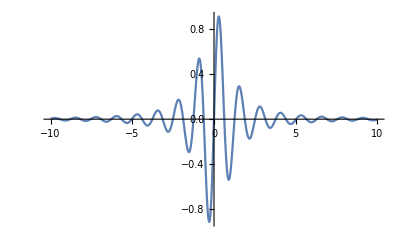

```mathematica
F1=Plot[Sin[5 * x]/(1 + x^2), {x, -10, 10}, PlotRange-> All]
```

F2

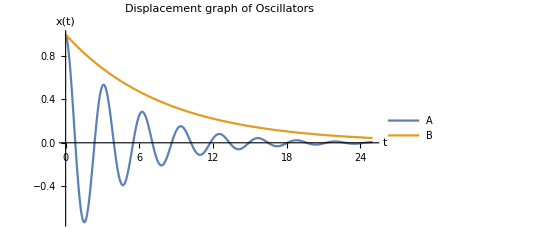

```mathematica
F2=Plot[{Exp[-t/5] * Cos[2 * t],Exp[-t/8]}, {t, 0, 25}, PlotLegends -> {"A", "B"}, AxesLabel -> {t, x[t]}, PlotLabel -> "Displacement graph of Oscillators"]
```

F3

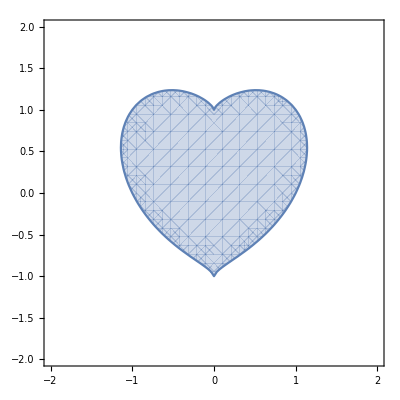

```mathematica
F3=RegionPlot[(x^2 + y ^2 - 1)^3 - x^2 * y^3 < 0, {x, -2, 2}, {y, -2, 2}]
```

F4

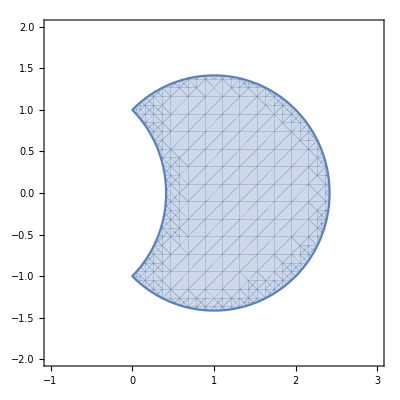

```mathematica
F4=RegionPlot[(x - 1)^2 + y^2 < 2 && (x + 1)^2 + y ^2 >2, {x, -1, 3}, {y, -2, 2}]
```

F5

```mathematica
F5=Plot3D[Exp[-Sqrt[x^2 + y ^2] / 8 * Cos[Sqrt[x^2 + y ^2]]], {x, -20, 20}, {y, -20, 20}]
```

-Graphics3D-

F6

```mathematica
PlotRegion[2 * x + 3 == 4^x, {x, -10, 10}]
```

PlotRegion[3+2 x==4^x,{x,-10,10}]

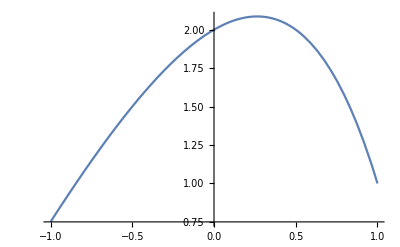

```mathematica
Plot[3+2 x==4^x,{x,-1,1}]
```

```mathematica
F6={{0.27388486981107363,2.0880747223290737}}
```

{{0.273885,2.08807}}

## G: Derivatives and Integrals

```mathematica
(*Run if you accidentally assigned values to some of the symbolic variables.*)
ClearAll[x,y,α,ϕ,β];
```

G1

```mathematica
G1=D[y^2 * Cos[y^8], y]
```

2 y Cos[y^8]-8 y^9 Sin[y^8]

G2

```mathematica
G2= D[Cos[1/ϕ], ϕ]
```

Sin[1/ϕ]/ϕ^2

G3

```mathematica
G3=ReplaceAll[D[α^3 / (1 + α^4), α] ,{α -> 2}]
```

-52/289

G4

```mathematica
G4=Integrate[β^n, β]
```

β^(1+n)/(1+n)

G5

```mathematica
G5=Integrate[1/(x^2 - 1)^2, x]
```

1/4 (-(2 x)/(-1+x^2)-Log[1-x]+Log[1+x])

## H: Manipulate

```mathematica
(*Run if you accidentally assigned values to some of the symbolic variables.*)
ClearAll[x,y,g,t,A,f,p];
```

H1

```mathematica
H1=Manipulate[x * (1 + g )^(y),{{x, 100}, 0, 1000},{{y, 10}, 0, 25}, {{g, 9.2}, 0, 12}]
```

H2

```mathematica
Wave[t_, A_, f_, p_]:= A * Sin[2 * Pi * f * t + p]
```

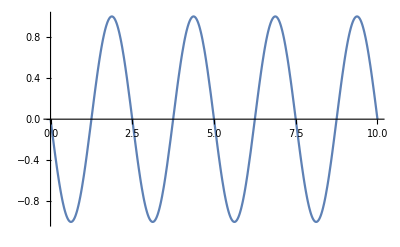

```mathematica
H2=Plot[Wave[t, 1, 0.4, Pi],{t, 0, 10}]
```

H3

```mathematica
H3=Manipulate[Plot[Wave[t, A, f, p],{t, 0, 10}, PlotRange-> 2.2],{A,0.5, 2}, {f,0.1,1}, {p, 0, 2 * Pi}]
```

#### Check assignments

When you are done, run the entire notebook using Evaluation→Evaluate Notebook from the menu bar. The code below will print a list of the questions you did not answer, or forgot to assign to the correct variable.

```mathematica
qnames={"A1","A2","A3","A4","A5","A6","A7","A8","A9","A10","A11","B1","C1","C2","C3","C4","C5","D1","D2","D3","D4","D5","D6","E1","E2","E3","E4","F1","F2","F3","F4","F5","F6","G1","G2","G3","G4","G5","H1","H2","H3"};
undefined=Select[{#,ToExpression["ValueQ["<>#<>"]"]}& /@ qnames,!#[[2]]&][[All,1]];
Print[Row[{"Is your name: ",StudentName,"?"}]]
Print[Row[{"Is your student number: ",StudentNumber,"?"}]]
If[undefined=={},Print["All questions answered."],Row[{"The following questions were not answered: ",undefined}]]
```

Is your name: JL Gouws?

Is your student number: 26634554?

All questions answered.